## Matrix elements for the single-particle Hamiltonian h

Fromula:-Graphics-

Taken from: -Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
A=167;
j1=13/2;
j2=11/2;
coupling[j_,beta_]:=195/(j(j+1))A^(-1/3)beta;
hdiag[j_,k_,beta_,gamma_]:=1/2 coupling[j,beta]*Cos[gamma*π/180](k^2-1/3 j(j+1));
```

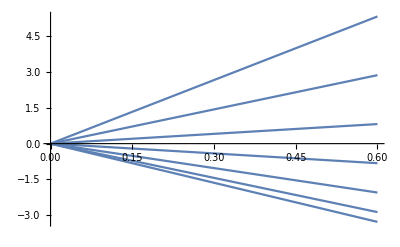

```mathematica
betaPlot[j_,gamma_]:=Plot[Table[hdiag[j,k,x,gamma],{k,1/2,j,1}],{x,0,0.6}];
betaPlot[j1,20]
```